```mathematica
myAxesSize=21;
myLabelSize=18;
myImageSize=1000;
SetDirectory[NotebookDirectory[]];
h={1,1/2,1/4,1/8,1/16};
```

## Poisson 0.3

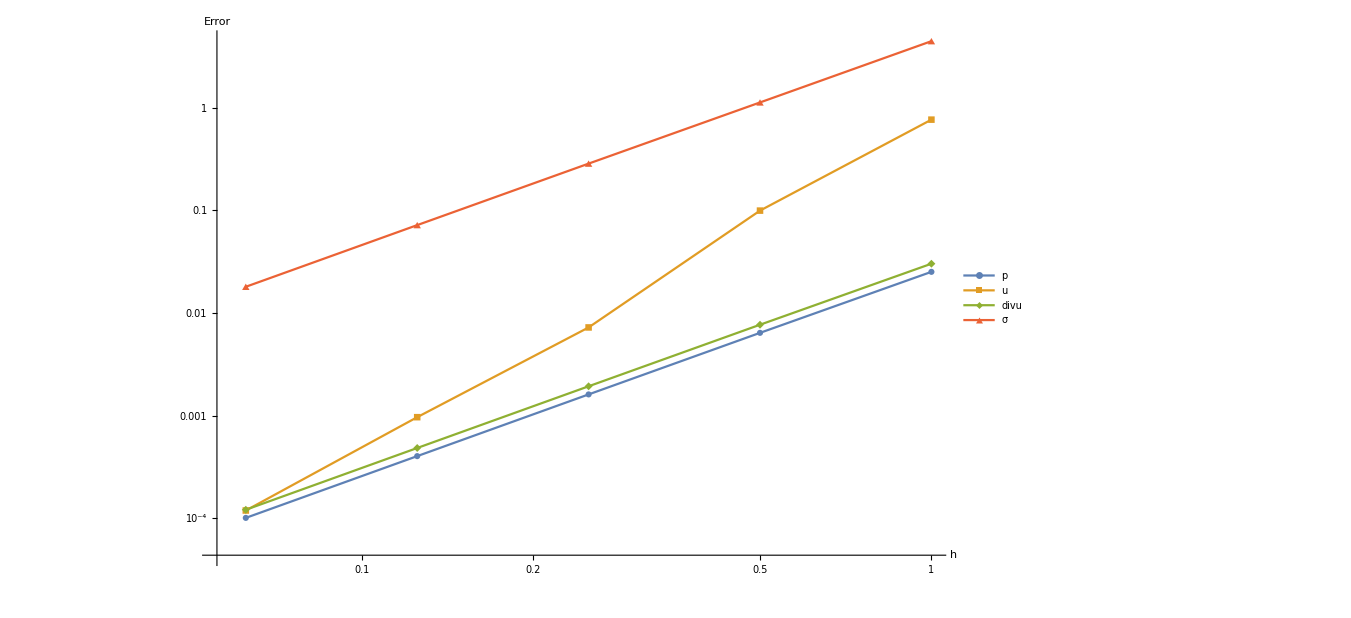

{1.97372,1.99179,1.99678,1.99808}

{2.94318,3.77958,2.90371,3.01951}

{1.97373,1.99178,1.99678,1.99807}

{1.98223,1.97897,1.98999,1.99501}

```mathematica
(*poisson=0.3*)
Errors1={0.0251797,0.62113,0.764558,532.949,0.0302157,0.745356,4.44299,65.7889};
Errors2={0.00641064,0.62113,0.0994091,524.069,0.00769276,0.745356,1.12451,57.3788};
Errors3={0.00161181,0.62113,0.00723868,521.84,0.00193418,0.745356,0.285255,55.0652};
Errors4={0.000403853,0.62113,0.000967288,521.285,0.000484624,0.745356,0.0718104,54.4707};
Errors5={0.000101098,0.62113,0.000119287,521.148,0.000121318,0.745356,0.0180148,54.3211};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.49

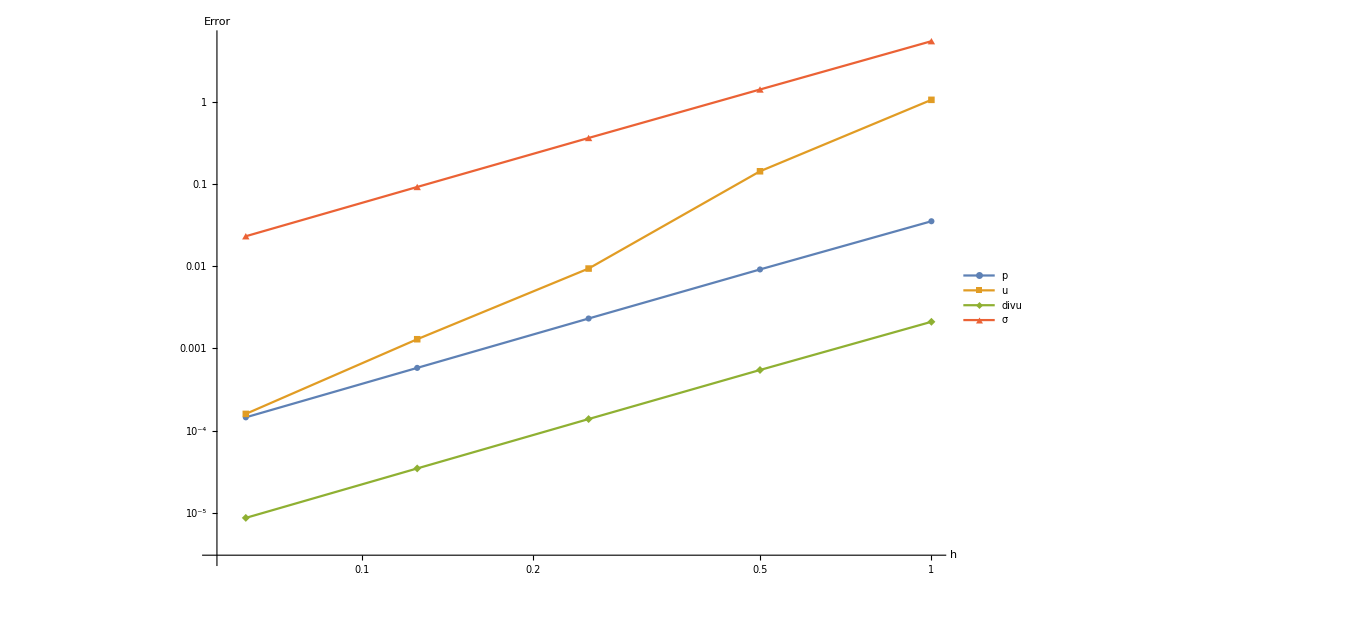

{1.94541,1.98076,1.99317,1.99612}

{2.88372,3.92656,2.85313,3.01429}

{1.94541,1.98076,1.99317,1.99612}

{1.9502,1.9569,1.97806,1.98892}

```mathematica
(*poisson=0.49*)
Errors1={0.0350839,0.62113,1.04819,532.662,0.00210503,0.0372678,5.40987,65.8037};
Errors2={0.00910921,0.62113,0.142021,524.115,0.000546553,0.0372678,1.39997,57.387};
Errors3={0.00230788,0.62113,0.00933984,521.967,0.000138473,0.0372678,0.360605,55.0692};
Errors4={0.000579709,0.62113,0.00129259,521.431,3.47826 10^-05,0.0372678,0.0915324,54.4733};
Errors5={0.000145318,0.62113,0.000159981,521.299,8.71906 10^-06,0.0372678,0.0230596,54.3232};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.4999

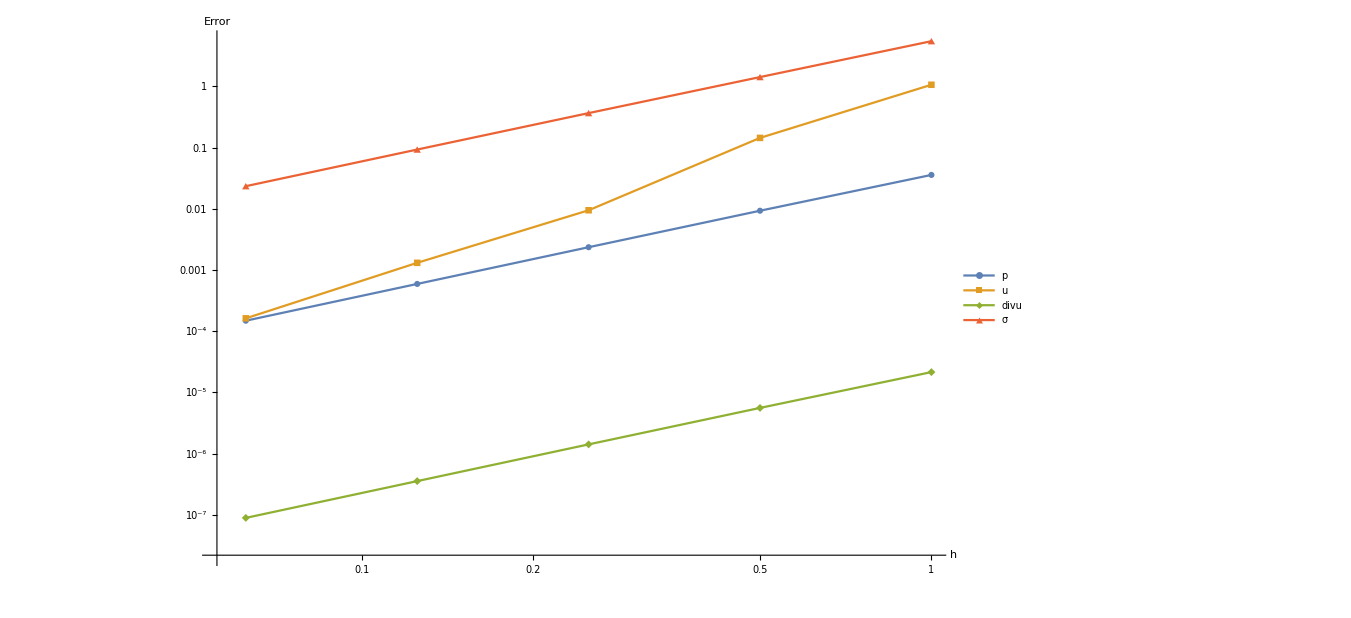

{1.94359,1.98014,1.99301,1.99606}

{2.88471,3.9283,2.85202,3.0137}

{1.9436,1.98014,1.99301,1.99607}

{1.94829,1.9559,1.97765,1.98866}

```mathematica
(*poisson=0.4999*)
Errors1={0.0358461,0.62113,1.06611,532.649,2.15077 10^-05,0.000372678,5.49263,65.8044};
Errors2={0.00931885,0.62113,0.14435,524.119,5.59131 10^-06,0.000372678,1.42327,57.3874};
Errors3={0.002362,0.62113,0.00948156,521.974,1.4172 10^-06,0.000372678,0.366861,55.0694};
Errors4={0.000593367,0.62113,0.00131322,521.44,3.5602 10^-07,0.000372678,0.0931469,54.4734};
Errors5={0.000148747,0.62113,0.000162601,521.308,8.92479 10^-08,0.000372678,0.0234705,54.3234};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.499999

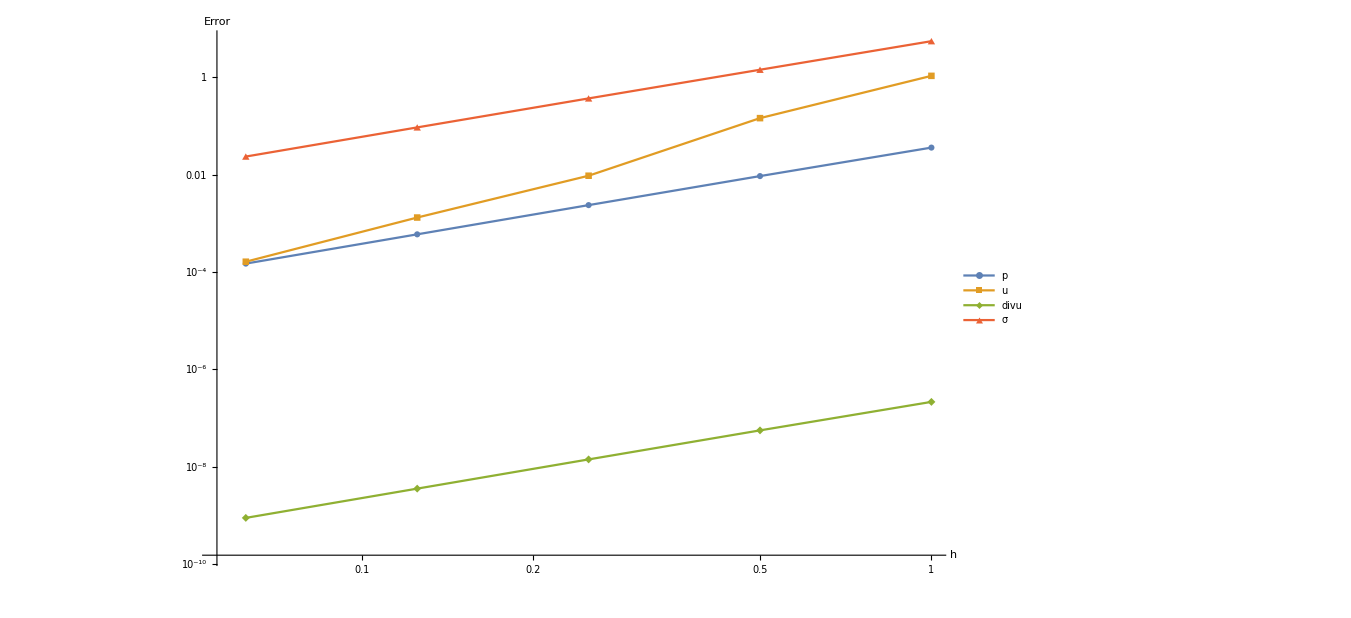

{1.94357,1.98014,1.99301,1.99607}

{2.88473,3.92831,2.852,3.0137}

{1.94358,1.98014,1.99302,1.99603}

{1.94827,1.95589,1.97765,1.98866}

```mathematica
(*poisson=0.499999*)
Errors1={0.0358539,0.62113,1.06629,532.648,2.15124 10^-07,3.72678 10^-06,5.49348,65.8044};
Errors2={0.009321,0.62113,0.144373,524.119,5.5926 10^-08,3.72678 10^-06,1.42351,57.3874};
Errors3={0.00236255,0.62113,0.009483,521.974,1.41753 10^-08,3.72678 10^-06,0.366926,55.0694};
Errors4={0.000593507,0.62113,0.00131343,521.44,3.56101 10^-09,3.72678 10^-06,0.0931635,54.4734};
Errors5={0.000148782,0.62113,0.000162627,521.308,8.92705 10^-10,3.72678 10^-06,0.0234747,54.3234};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.5

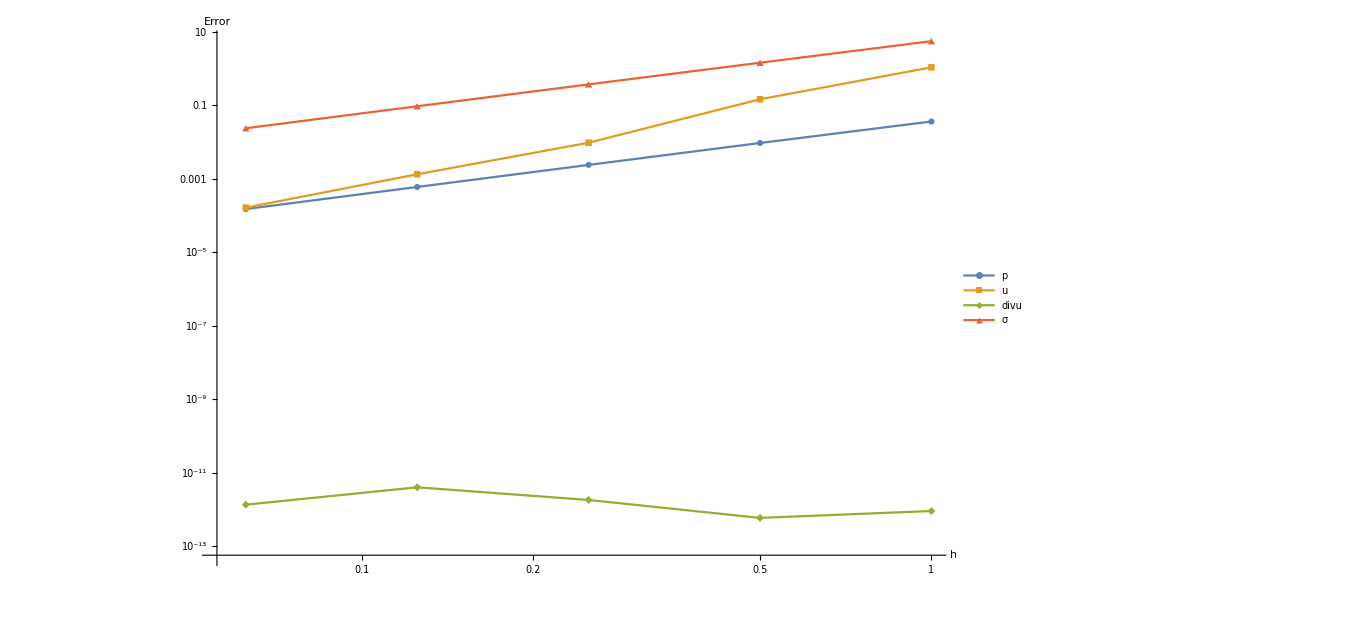

{1.94357,1.98014,1.99301,1.99607}

{2.88473,3.92832,2.85201,3.01369}

{0.621224,-1.61952,-1.14434,1.57056}

{1.94826,1.9559,1.97765,1.98866}

```mathematica
(*poisson=0.5*)
Errors1={0.035854,0.62113,1.0663,532.648,9.05734 10^-13,0,5.49349,65.8044};
Errors2={0.00932102,0.62113,0.144374,524.119,5.88835 10^-13,0,1.42352,57.3874};
Errors3={0.00236256,0.62113,0.00948302,521.974,1.80933 10^-12,0,0.366926,55.0694};
Errors4={0.000593508,0.62113,0.00131343,521.44,3.99944 10^-12,0,0.0931637,54.4734};
Errors5={0.000148782,0.62113,0.000162628,521.308,1.34652 10^-12,0,0.0234748,54.3234};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.4}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```